```mathematica
oscillator[d_,w0_,x_]:=Module[{w, phi, A, cos, exp,y},
w=Sqrt[w0^2-d^2];
phi=ArcTan[-d/w];
A=1/(2*Cos[phi]);
cos=Cos[w0*x+phi];
exp=Exp[-d*x];
y=exp*2*A*cos;
y//N
]
```

```mathematica
net[ninput_,noutput_,nhidden_,nlayers_]:=
NetChain[{
LinearLayer[nhidden],
FunctionLayer[Tanh],
Table[{
LinearLayer[nhidden],Tanh},
{nlayers}],
LinearLayer[noutput]
}, "Input"->{ninput}]
```

```mathematica
firstnet=net[1,1,10,2]
```

NetChain[<>]

```mathematica
firstnet = NetInsertSharedArrays[firstnet]
```

NetChain[<>]

```mathematica
firstnet = NetInitialize[firstnet]
```

NetChain[<>]

```mathematica
firstnet[12]
```

{0.0365571}

```mathematica
ploss = NetGraph[
<|
"d1" -> FunctionLayer[Apply[(#2 - #1)/ 10^-3&]],
"d2" ->  FunctionLayer[Apply[(#2 - #1)/ 10^-3&]],
"total"-> TotalLayer[],
"sum" ->SummationLayer[]
|>, 
{
NetPort["YHPhys"]->"d1",
NetPort["yHPhys"]->"d1", 
"d1" -> "total",
"d1" -> "d2",
NetPort["yHPhys"] -> "d2",
"d2" ->"total",
"total" -> "sum"
}
]
```

NetGraph[<>]

```mathematica
InitialNetPhys= NetGraph[
<|
"pNet" -> firstnet,
"deltaPNet"-> firstnet,
"xplusdelta"-> FunctionLayer[Apply[#+10^-3&]],
"physicsLoss"->ploss,
"total" -> TotalLayer[]
|>,
 {
NetPort["xPhys"] -> "pNet" ,
NetPort["xPhys"] -> "xplusdelta" -> "deltaPNet" ,
{"deltaPNet", "pNet"}-> "physicsLoss"
}
]
```

NetGraph[<>]

```mathematica
InitialNetPhys = NetInitialize[InitialNetPhys]
```

NetGraph[<>]

```mathematica
TotalPhysicalLoss=RootMeanSquare@ Table[InitialNetPhys[x],{x, 0, 1, 0.001}]
```

68.2557

```mathematica
InitialNet= NetGraph[
<|
"net"-> firstnet,
"loss1"-> MeanSquaredLossLayer[],
"physloss" -> NetArrayLayer["Array"-> Evaluate@TotalPhysicalLoss, "Output"->1]

|>,
 {
NetPort["xData"]-> "net",
"net" -> "loss1"-> NetPort["loss1"],
"physloss"-> NetPort["physloss"]
}
]
```

NetGraph[<>]

```mathematica
Shuffle[x_]:= RandomChoice[x, Length[x]]
```

```mathematica
data=Table[{x,oscillator[2,20,x]},{x,0,0.5,0.05}];
traindata =Table[{data[[i]][[1]]}-> data[[i]][[2]], {i, 1, Length[data]}];
traindata = RandomChoice[traindata, Length[traindata]]
```

{{0.3}→0.511541,{0.5}→-0.328791,{0.5}→-0.328791,{0.25}→0.113595,{0.2}→-0.489136,{0.35}→0.407166,{0.4}→-0.0206987,{0.15}→-0.722897,{0.4}→-0.0206987,{0.15}→-0.722897,{0.35}→0.407166}

```mathematica
data[[1]][[1]]
```

0.

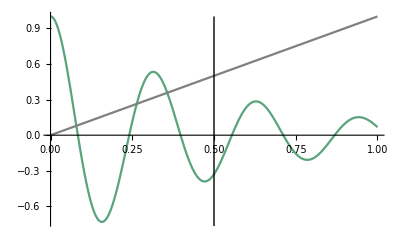

```mathematica
Show[
Plot[oscillator[2,20,x],{x,0,1}, ColorFunction->Hue],
Plot[HopefullyFinalNet[[1]][i], {i,0,1}, PlotStyle->Gray],
Graphics@Line[{{0.5, -1}, {0.5, 1}}]
]
```